```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
controlColor=Black;
```

```mathematica
dateMouseListControl={{"012122","Mouse22550"},{"012822","Mouse22549"},{"121621","Mouse22525"},{"121721","Mouse22599"},{"011122","Mouse22598"},{"032923","Mouse23149"},{"033023","Mouse23128"},{"033123","Mouse23149"},{"070323","Mouse23149"},{"070423","Mouse23128"},{"070723","Mouse23128"}};
```

```mathematica
(***V1 axons, eOPN3***)
```

```mathematica
dateMouseListV1axons={{"012722","Mouse22504"},{"121821","Mouse22485"},{"062723","Mouse23154"},{"062723","Mouse23182"},{"063023","Mouse23154"},{"063023","Mouse23182"}};
```

```mathematica
(***LP axons, eOPN3***)
```

```mathematica
dateMouseListLPaxons={{"050123","Mouse23133"},{"050123","Mouse23142"},{"050323","Mouse23133"},{"050323","Mouse23142"},{"051823","Mouse23198"},{"052623","Mouse23198"},{"052623","Mouse23105"},{"062923","Mouse23139"},{"070223","Mouse23139"}};
```

```mathematica
(***LM axons, eOPN3***)
```

```mathematica
dateMouseListLMaxons={{"062623","Mouse23152"},{"062823","Mouse23152"},{"062923","Mouse23190"},{"070123","Mouse23190"},{"070723","Mouse23666"},{"071223","Mouse23666"}};
```

```mathematica
(************************************)
```

```mathematica
pairedROIsListControl=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListControl]}];
```

```mathematica
pairedROIsListV1axons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
pairedROIsListLPaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
pairedROIsListLMaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
(***Before-After paired loc mod indices***)
```

```mathematica
pairedWhiskModIndexSummaryValsControl=ToExpression/@Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/","/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_","whiskerModPaired_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListControl[[n]]}],{n,1,Length[dateMouseListControl]}],1][[All,2]];
```

```mathematica
pairedWhiskModIndexSummaryValsV1axons=ToExpression/@Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/","/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_","whiskerModPaired_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}],1][[All,2]];
```

```mathematica
pairedWhiskModIndexSummaryValsLPaxons=ToExpression/@Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/","/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_","whiskerModPaired_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}],1][[All,2]];
```

```mathematica
pairedWhiskModIndexSummaryValsLMaxons=ToExpression/@Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/","/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_","whiskerModPaired_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}],1][[All,2]];
```

```mathematica
(***************************************************)
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S7G****************) 
(**********************************************)
```

```mathematica
diffsWhiskControl=Table[(pairedWhiskModIndexSummaryValsControl[[n,2]]-pairedWhiskModIndexSummaryValsControl[[n,1]]),{n,1,Length[pairedWhiskModIndexSummaryValsControl]}];
```

```mathematica
diffsWhiskV1axons=Table[(pairedWhiskModIndexSummaryValsV1axons[[n,2]]-pairedWhiskModIndexSummaryValsV1axons[[n,1]]),{n,1,Length[pairedWhiskModIndexSummaryValsV1axons]}];
```

```mathematica
diffsWhiskLPaxons=Table[(pairedWhiskModIndexSummaryValsLPaxons[[n,2]]-pairedWhiskModIndexSummaryValsLPaxons[[n,1]]),{n,1,Length[pairedWhiskModIndexSummaryValsLPaxons]}];
```

```mathematica
diffsWhiskLMaxons=Table[(pairedWhiskModIndexSummaryValsLMaxons[[n,2]]-pairedWhiskModIndexSummaryValsLMaxons[[n,1]]),{n,1,Length[pairedWhiskModIndexSummaryValsLMaxons]}];
```

```mathematica
(******************)
```

```mathematica
controlWhiskModPairsPlotPts=Partition[Riffle[{0.4,0.6} ,#],2]&/@pairedWhiskModIndexSummaryValsControl;
```

```mathematica
allWhiskModsControlDark=pairedWhiskModIndexSummaryValsControl[[All,1]];
```

```mathematica
allWhiskModsControlLED=pairedWhiskModIndexSummaryValsControl[[All,2]];
```

```mathematica
bin=2*InterquartileRange[allWhiskModsControlDark]*(Length[allWhiskModsControlDark]^(-1/3))
```

0.0134082

```mathematica
minVal=Min[Join[allWhiskModsControlDark,allWhiskModsControlLED]];
```

```mathematica
maxVal=Max[Join[allWhiskModsControlDark,allWhiskModsControlLED]];
```

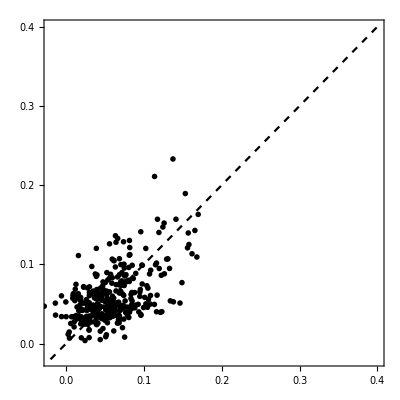

```mathematica
Show[ListPlot[pairedWhiskModIndexSummaryValsControl,PlotRange->{{-0.02,0.4},{-0.02,0.4}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{controlColor,PointSize[0.01]},FrameTicks->{{LinTicks[-0.02,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.02,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,-0.02,0.4},PlotStyle->{Black,Dashed}]]
```

```mathematica
(*******************************************)
```

```mathematica
v1AxonsWhiskModPairsPlotPts=Partition[Riffle[{0.4,0.6} ,#],2]&/@pairedWhiskModIndexSummaryValsV1axons;
```

```mathematica
allWhiskModsV1axonsDark=pairedWhiskModIndexSummaryValsV1axons[[All,1]];
```

```mathematica
allWhiskModsV1axonsLED=pairedWhiskModIndexSummaryValsV1axons[[All,2]];
```

```mathematica
minVal=Min[Join[allWhiskModsV1axonsDark,allWhiskModsV1axonsLED]];
```

```mathematica
maxVal=Max[Join[allWhiskModsV1axonsDark,allWhiskModsV1axonsLED]];
```

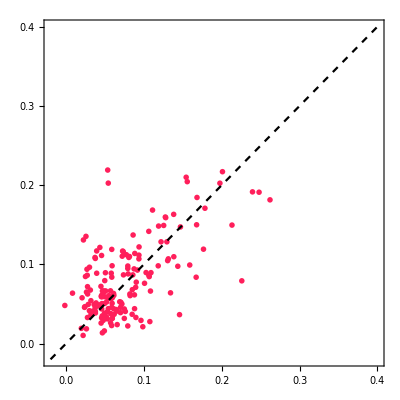

```mathematica
Show[ListPlot[pairedWhiskModIndexSummaryValsV1axons,PlotRange->{{-0.02,0.4},{-0.02,0.4}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{v1Color,PointSize[0.01]},FrameTicks->{{LinTicks[-0.02,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.02,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,-0.02,0.4},PlotStyle->{Black,Dashed}]]
```

```mathematica
(*******************************************)
```

```mathematica
lpAxonsWhiskModPairsPlotPts=Partition[Riffle[{0.4,0.6} ,#],2]&/@pairedWhiskModIndexSummaryValsLPaxons;
```

```mathematica
allWhiskModsLPaxonsDark=pairedWhiskModIndexSummaryValsLPaxons[[All,1]];
```

```mathematica
allWhiskModsLPaxonsLED=pairedWhiskModIndexSummaryValsLPaxons[[All,2]];
```

```mathematica
minVal=Min[Join[allWhiskModsLPaxonsDark,allWhiskModsLPaxonsLED]];
```

```mathematica
maxVal=Max[Join[allWhiskModsLPaxonsDark,allWhiskModsLPaxonsLED]];
```

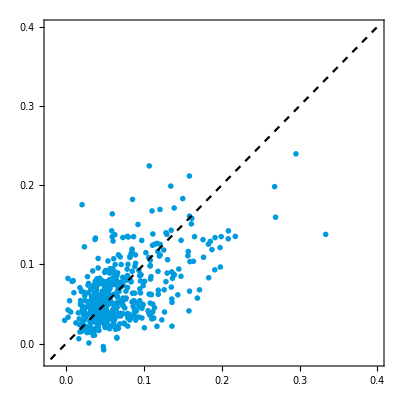

```mathematica
Show[ListPlot[pairedWhiskModIndexSummaryValsLPaxons,PlotRange->{{-0.02,0.4},{-0.02,0.4}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{lpColor,PointSize[0.01]},FrameTicks->{{LinTicks[-0.02,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.02,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,-0.02,0.4},PlotStyle->{Black,Dashed}]]
```

```mathematica
(*******************************************)
```

```mathematica
lmAxonsWhiskModPairsPlotPts=Partition[Riffle[{0.4,0.6} ,#],2]&/@pairedWhiskModIndexSummaryValsLMaxons;
```

```mathematica
allWhiskModsLMaxonsDark=pairedWhiskModIndexSummaryValsLMaxons[[All,1]];
```

```mathematica
allWhiskModsLMaxonsLED=pairedWhiskModIndexSummaryValsLMaxons[[All,2]];
```

```mathematica
minVal=Min[Join[allWhiskModsLMaxonsDark,allWhiskModsLMaxonsLED]];
```

```mathematica
maxVal=Max[Join[allWhiskModsLMaxonsDark,allWhiskModsLMaxonsLED]];
```

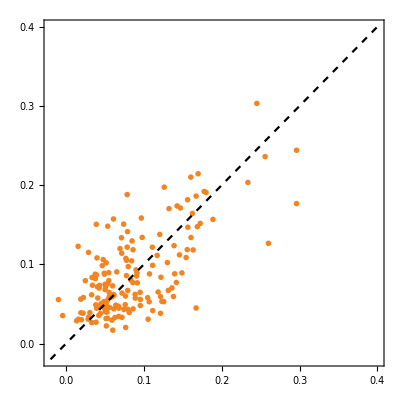

```mathematica
Show[ListPlot[pairedWhiskModIndexSummaryValsLMaxons,PlotRange->{{-0.02,0.4},{-0.02,0.4}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{lmColor,PointSize[0.01]},FrameTicks->{{LinTicks[-0.02,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.02,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,-0.02,0.4},PlotStyle->{Black,Dashed}]]
```

```mathematica
(***********************************************************)
```

```mathematica
(************)
```

```mathematica
bin=2*InterquartileRange[diffsWhiskControl]*(Length[diffsWhiskControl]^(-1/3))
```

0.012627

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{diffsWhiskControl},{-0.42,0.42,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{controlColor}),PerformanceGoal->"Speed",PlotRange->{{-0.42,0.42},{0,0.22}}];
```

```mathematica
h2=Histogram[{diffsWhiskControl},{-0.42,0.42,bin},hfn,ChartStyle->{{controlColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.42,0.42},{0,0.22}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

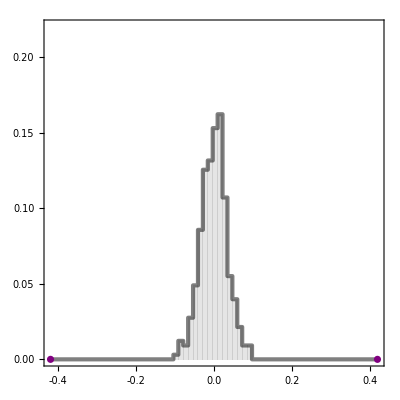

```mathematica
histModIndexControl=Show[hline,h2,ListPlot[{{-0.42,0},{0.42,0}},PlotStyle->Purple],PlotRange->{{-0.42,0.42},{0,0.22}},FrameTicks->{{LinTicks[0,0.22,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.42,0.42,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
bin=2*InterquartileRange[diffsWhiskV1axons]*(Length[diffsWhiskV1axons]^(-1/3))
```

0.0172619

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{diffsWhiskV1axons},{-0.42,0.42,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{v1Color}),PerformanceGoal->"Speed",PlotRange->{{-0.42,0.42},{0,0.22}}];
```

```mathematica
h2=Histogram[{diffsWhiskV1axons},{-0.42,0.42,bin},hfn,ChartStyle->{{v1Color},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.42,0.42},{0,0.22}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

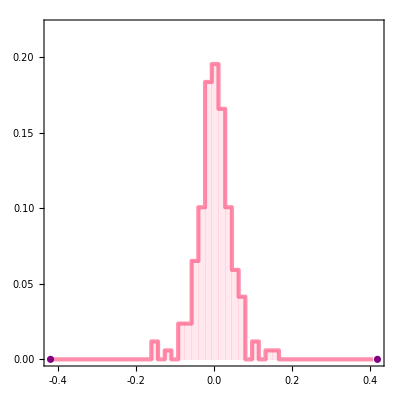

```mathematica
histModIndexV1axons=Show[hline,h2,ListPlot[{{-0.42,0},{0.42,0}},PlotStyle->Purple],PlotRange->{{-0.42,0.42},{0,0.22}},FrameTicks->{{LinTicks[0,0.22,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.42,0.42,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
bin=2*InterquartileRange[diffsWhiskLPaxons]*(Length[diffsWhiskLPaxons]^(-1/3))
```

0.0114693

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{diffsWhiskLPaxons},{-0.42,0.42,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{lpColor}),PerformanceGoal->"Speed",PlotRange->{{-0.42,0.42},{0,0.22}}];
```

```mathematica
h2=Histogram[{diffsWhiskLPaxons},{-0.42,0.42,bin},hfn,ChartStyle->{{lpColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.42,0.42},{0,0.22}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

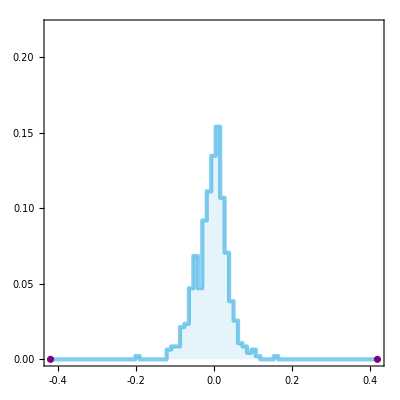

```mathematica
histModIndexLPaxons=Show[hline,h2,ListPlot[{{-0.42,0},{0.42,0}},PlotStyle->Purple],PlotRange->{{-0.42,0.42},{0,0.22}},FrameTicks->{{LinTicks[0,0.22,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.42,0.42,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
bin=2*InterquartileRange[diffsWhiskLMaxons]*(Length[diffsWhiskLMaxons]^(-1/3))
```

0.0209539

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{diffsWhiskLMaxons},{-0.42,0.42,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{lmColor}),PerformanceGoal->"Speed",PlotRange->{{-0.42,0.42},{0,0.22}}];
```

```mathematica
h2=Histogram[{diffsWhiskLMaxons},{-0.42,0.42,bin},hfn,ChartStyle->{{lmColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.42,0.42},{0,0.22}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

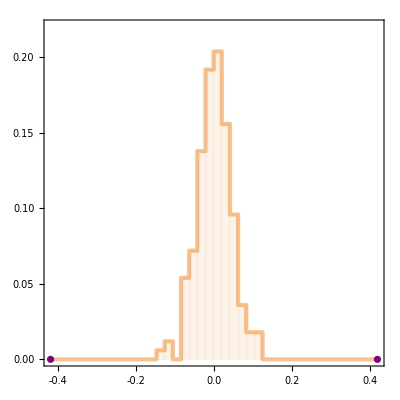

```mathematica
histModIndexLMaxons=Show[hline,h2,ListPlot[{{-0.42,0},{0.42,0}},PlotStyle->Purple],PlotRange->{{-0.42,0.42},{0,0.22}},FrameTicks->{{LinTicks[0,0.22,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.42,0.42,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S7H****************) 
(**********************************************)
```

```mathematica
controlCharts=Show[BoxWhiskerChart[diffsWhiskControl,{{"Whiskers", Directive[Darker@controlColor,Thick]}, {"Fences", Directive[Darker@controlColor,Thick]},{"MedianMarker", Directive[Darker@controlColor,Thickness[0.009]]}},PlotRange->{All,{-0.2,0.2}},ChartStyle->Directive[controlColor,Opacity[0.3]],Frame->False],DistributionChart[diffsWhiskControl,PlotRange->{All,{-0.2,0.2}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],controlColor],Frame->False],FrameTicks->{{LinTicks[-0.2,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[diffsWhiskV1axons,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{-0.2,0.2}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[diffsWhiskV1axons,PlotRange->{All,{-0.2,0.2}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[-0.2,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[diffsWhiskLPaxons,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{-0.2,0.2}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[diffsWhiskLPaxons,PlotRange->{All,{-0.2,0.2}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[-0.2,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[diffsWhiskLMaxons,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{-0.2,0.2}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[diffsWhiskLMaxons,PlotRange->{All,{-0.2,0.2}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[-0.2,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[diffsWhiskControl,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-0.2,0.2}},ChartStyle->Transparent,Frame->False],DistributionChart[diffsWhiskControl,PlotRange->{All,{-0.2,0.2}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-0.2,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

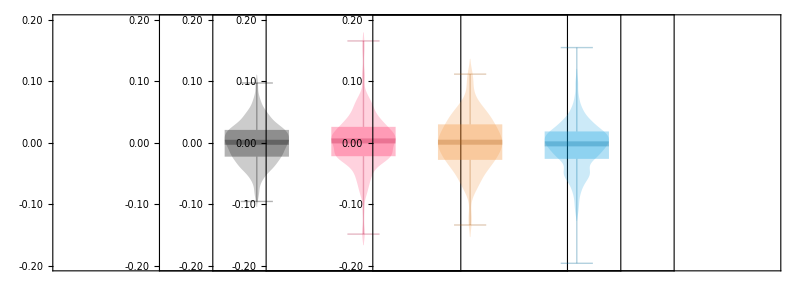

```mathematica
GraphicsRow[{controlCharts,v1AxonCharts,lmAxonCharts,lpAxonCharts,transp},Spacings->{{-280,-280,-280,-280,-480}}]
```